## DPS equation

```mathematica
multipliers = {(ad/36), Piecewise[{{2,crit ≥ 5000}}, 1 + (crit/5000)], Piecewise[{{5/2,aspd ≥ 5000}}, 1 + (aspd/3333)]};
dps = Times@@multipliers
multipliersE = {(ad/36), Piecewise[{{2,crit ≥ 5000}}, 1 + (crit/5000)], 5/2};
dpsE = Times@@multipliersE
```

1/36 ad (Piecewise[{{2, crit≥5000}, {1+crit/5000, True}}]) (Piecewise[{{5/2, aspd≥5000}, {1+aspd/3333, True}}])

5/72 ad (Piecewise[{{2, crit≥5000}, {1+crit/5000, True}}])

```mathematica
constraints = {ad ≥ 0, crit ≥ 0, aspd ≥ 0, crit ≤ 5000, aspd + ad + crit == 10000};
{knownBestDPS,knownBestDistro} = Maximize[{dps,constraints}, {ad,crit,aspd}]
```

{8452264653/22220000,{ad→6111,crit→1111,aspd→2778}}

## Path of steepest ascent

```mathematica
g = Grad[dps /. {ad -> x, crit -> y, aspd -> z}, {x,y,z}]
gE = Grad[dpsE /. {ad -> x, crit -> y}, {x,y}]
```

{1/36 (Piecewise[{{2, y≥5000}, {1+y/5000, True}}]) (Piecewise[{{5/2, z≥5000}, {1+z/3333, True}}]),1/36 x (Piecewise[{{5/2, z≥5000}, {1+z/3333, True}}]) (Piecewise[{{1/5000, y<5000}, {0, y>5000}, {Indeterminate, True}}]),1/36 x (Piecewise[{{2, y≥5000}, {1+y/5000, True}}]) (Piecewise[{{1/3333, z<5000}, {0, z>5000}, {Indeterminate, True}}])}

{5/72 (Piecewise[{{2, y≥5000}, {1+y/5000, True}}]),5/72 x (Piecewise[{{1/5000, y<5000}, {0, y>5000}, {Indeterminate, True}}])}

```mathematica
{{ad2critUnbounded,ad2aspdUnbounded}} = {y[x],z[x]} /. DSolve[{
	y'[x] == (g[[1]] /. y -> y[x]) / (g[[2]] /. y -> y[x]), 
	z'[x] == (g[[1]] /. {y -> y[x], z -> z[x]}) / (g[[3]] /. {y -> y[x], z -> z[x]}),
	y[ad /. knownBestDistro] == (crit /. knownBestDistro),
	z[ad /. knownBestDistro] == (aspd /. knownBestDistro)}, 
	{y[x],z[x]}, x]

ad2crit[attack_] := Max[0,ad2critUnbounded] /. x -> attack
ad2aspd[attack_] := Max[0,ad2aspdUnbounded] /. x -> attack


{{ad2critUnboundedE}} = {y[x]} /. DSolve[{
	y'[x] == (g[[1]] /. y -> y[x]) / (g[[2]] /. y -> y[x]), 
	y[ad /. knownBestDistro] == (crit /. knownBestDistro)}, 
	{y[x]}, x]

ad2critE[attack_] := Max[0,ad2critUnboundedE] /. x -> attack
```

Power::infy: Infinite expression 1/0 encountered.

{{ConditionalExpression[-5000+x,(Im[Log[x]]==0&&Re[Log[x]]≤4 Log[2]+4 Log[5])||Im[Log[x]]==π],ConditionalExpression[-3333+x,(Im[Log[x]]==0&&Re[Log[x]]≤Log[13]+Log[641])||Im[Log[x]]==π]}}

Power::infy: Infinite expression 1/0 encountered.

{{ConditionalExpression[-5000+x,(Im[Log[x]]==0&&Re[Log[x]]≤4 Log[2]+4 Log[5])||Im[Log[x]]==π]}}

```mathematica
(* rewrite 'gADodd' in terms of Piecewise because ConditionalExpression interacts oddly*)
gADodd = x /. Solve[{ad2crit[x] + ad2aspd[x] + Max[0,x] == h, h ≥ 0}, x, 
					Method -> Reduce]
gADfixed = Piecewise[gADodd /. ConditionalExpression[xx_, yy_] :> {xx, yy}]

gAD[gold_] := Assuming[x ∈ Reals, FullSimplify[gADfixed /. h -> gold]]
gCrit[h_] := ad2crit[gAD[h]]
gAspd[h_] := ad2aspd[gAD[h]]

(* rewrite 'gADodd' in terms of Piecewise because ConditionalExpression interacts oddly*)
(*16666 gold: {ad->8333.,crit->3333.,aspd->5000.}*)
gADoddE = x /. Solve[{ad2critE[x] + 5000 + x == h, x > 8333, h ≥ 16666}, x, Method -> Reduce]
gADfixedE = Piecewise[gADoddE /. ConditionalExpression[xx_, yy_] :> {xx, yy}]

gADE[gold_] := Assuming[x ∈ Reals, FullSimplify[gADfixedE /. h -> gold]]
gCritE[h_] := Assuming[x ∈ Reals, FullSimplify[ad2critE[gADE[h]]]]

gADFull[h_] := Piecewise[{{gAD[h],h ≤ 16666}, {gADE[h], h < 20000}}, gADE[20000] + (h - 20000)]
gCritFull[h_] := Piecewise[{{gCrit[h],h ≤ 16666}, {gCritE[h], h < 20000}}, 5000]
gAspdFull[h_] := Piecewise[{{gAspd[h],h ≤ 16666}}, 5000]



gAspdFull[15000.0]
gAspdFull[18000]
gAspdFull[20000]
gAspdFull[25000]
```

Solve::fexp: Warning: Solve used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

{ConditionalExpression[h,x∈Reals&&0<h≤3333],ConditionalExpression[(3333+h)/2,x∈Reals&&3333<h≤6667],ConditionalExpression[(8333+h)/3,x∈Reals&&6667<h≤16666]}

Piecewise[{{h, x∈Reals&&0<h≤3333}, {(3333+h)/2, x∈Reals&&3333<h≤6667}, {(8333+h)/3, x∈Reals&&6667<h≤16666}, {0, True}}]

Solve::fexp: Warning: Solve used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

{ConditionalExpression[h/2,x∈Reals&&16666<h≤20000]}

Piecewise[{{h/2, x∈Reals&&16666<h≤20000}, {0, True}}]

4444.67

5000

5000

5000

```mathematica
Plot[{gADFull[u], gCritFull[u], gAspdFull[u]}, {u, 0, 30000}, 
	PlotLegends -> "Expressions", 
	PlotStyle -> {Directive[Black, Thick], 
				  Directive[Dashed, Red, Thickness[0.015]], 
                  Directive[Blue, Thickness[0.015], Dashing["Large"]]}]

Plot[{Derivative[1][gADFull][u], Derivative[1][gCritFull][u], Derivative[1][gAspdFull][u]}, {u, 0, 30000}, 
	PlotLegends -> "Expressions", 
    PlotStyle -> {Directive[Black, Thick], 
				  Directive[Dashed, Red, Thickness[0.015]], 
				  Directive[Blue, Thickness[0.015], Dashing["Large"]]}]

Show[
  VectorPlot3D[g, {x, 0, 10000}, {y, 0, 10000}, {z, 0, 10000}, 
	VectorPoints -> Coarse, 
	AxesLabel -> {ad, crit, aspd}], 

  ParametricPlot3D[{gADFull[u], gCritFull[u], gAspdFull[u]}, {u, 0, 30000}, 
	PlotStyle -> Directive[Red, Thick]]
]
```

```mathematica
r = 25000;

SetOptions[Plot3D, 
			Mesh -> None, 
			ClippingStyle -> Black, 
			PlotStyle -> Directive[Green, Opacity[0.3], Specularity[White, 20]], 
			ColorFunctionScaling -> False,	
PlotRange -> {{0,7000},{0,7000},{0,7000}},
			ColorFunction -> ({x,y,z} ↦ ColorData["Thermometer"][Rescale[z,{0,r},{0,1}]])];

step = 1000
data = Flatten[Table[{crit,aspd,ad,dps}, {crit,0,r,step}, {aspd,0,r,step}, {ad, 0, r, step}], 2];
graph = Show[

ListPointPlot3D[List /@ data[[All, {1, 2, 3}]], 
 RegionFunction-> Function[{x,y,z}, x + y + z ≤ r],
 PlotStyle -> ({PointSize[Large], 
      Blend[{{0, Opacity[0.1,Darker[Blue]]}, {600, Opacity[0.2,Yellow]}, {1500, Opacity[0.5,Red]}}, #1]} & /@ Flatten[data[[All, {4}]]])],

ParametricPlot3D[{gCritFull[u], gAspdFull[u], gADFull[u]}, {u,0,r},  
		PlotStyle -> Directive[Green, Thickness[0.005], Opacity[0.8]],
		Mesh -> None,
		BoundaryStyle -> None],


	AxesLabel-> {"Crit (gold)","Aspd (gold)","AD (gold)"}, 	
	Boxed -> True,
	BoxStyle -> Directive[Dotted]
];
dps /. {ad -> gADFull[u], crit -> gCritFull[u], aspd -> gAspdFull[u]} /. u -> 15000.0


graph
```

1000

784.224

-Graphics3D-

```mathematica
"
```

## Comparison against gradient ascent results

```mathematica
threshold = 92.58 * 36
old[u_] := Assuming[x ∈ Reals, FullSimplify[{ad -> gADFull[u], crit -> gCritFull[u], aspd -> gAspdFull[u]}]]
new[u_] := Piecewise[{
	{{ad -> u, crit -> 0, aspd -> 0}, u ≤ threshold},
	{{ad -> threshold, crit -> 0, aspd -> u-threshold}, u-threshold < 5000},
	{{ad -> threshold, crit -> u-threshold-5000, aspd -> 5000}, u-threshold < 10000},
	{{ad -> u-10000, crit -> 5000, aspd -> 5000}, True}
	}]
```

3332.88

func | dps | gold distribution | sum | multipliers
old | 92.58 | ad→3332.88
crit→0.
aspd→0. | 3332.88 | 92.58
1.
1.
new | 92.58 | ad→3332.88
crit→0.
aspd→0. | 3332.88 | 92.58
1.
1.

func | dps | gold distribution | sum | multipliers
old | 144.679 | ad→4166.5
crit→0.
aspd→833.5 | 5000 | 115.736
1.
1.25008
new | 138.887 | ad→3332.88
crit→0.
aspd→1667.12 | 5000. | 92.58
1.
1.50019

func | dps | gold distribution | sum | multipliers
old | 784.224 | ad→7777.67
crit→2777.67
aspd→4444.67 | 15000 | 216.046
1.55553
2.33353
new | 694.444 | ad→5000.
crit→5000.
aspd→5000. | 15000 | 138.889
2.
2.5

{{0,AD},{3333,AD,AS},{6667,AD,AS,CRIT},{16666,AD,CRIT},{20000,AD}}

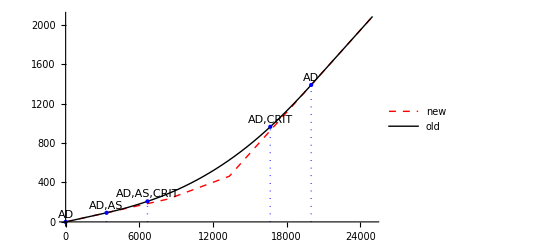

```mathematica
tab[u_] := {{"func", "dps", "gold distribution", "sum", "multipliers"},
			{"old",N[dps]/. old[u], N@old[u], {ad+crit+aspd}/. old[u], N@(multipliers /. old[u])} , 
			{"new", N[dps]/. new[u], N@new[u], {ad+crit+aspd}/. new[u], N@(multipliers /. new[u]) }}
tab[threshold] // TableForm
tab[5000] // TableForm
tab[15000] // TableForm

interestingPoints = {{0,"AD"},{3333,"AD,AS"},{6667,"AD,AS,CRIT"},{16666,"AD,CRIT"},{20000,"AD"}}

Show[
Plot[{dps /. new[u], dps /. old[u]}, {u,0,25000}, 
	PlotStyle -> {Directive[Dashed,Red,Thick], 
				 Directive[Black,Thick]}, 
	PlotLegends -> {new,old}],
ListPlot[Labeled[{#[[1]], dps /. old[#[[1]]]}, #[[2]], Top] &/@ interestingPoints, Filling -> Axis, FillingStyle-> Directive[Blue,Thick,Dotted], PlotStyle -> Directive[Blue,PointSize[Medium]]]
]
```

0. | 0. | 0.
92.5833 | 0. | 0.
138.889 | 0. | 0.50015
231.472 | 0.6666 | 1.50015
277.778 | 1. | 1.50015

0. | 0. | 0.
92.5833 | 0. | 0.
138.889 | 0. | 0.50015
231.472 | 0.6666 | 1.50015
277.778 | 1. | 1.50015

{ad→6111,crit→1111,aspd→2778}

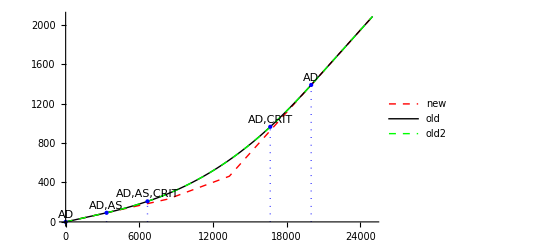

```mathematica
(*
vals[h_] := (old[h] /. ((a_->b_) -> b)) / {36.0, 5000.0, 3333.0}
vals /@ interestingPoints // TableForm
*)


old2[u_] := Thread[{ad,crit,aspd} -> Piecewise[{{{0,0,0}, u≤0}, {{-10000+u,5000,5000}, u≥20000}, {{u/2,-5000+u/2,5000}, 16666<u<20000}, {{u,0,0}, 0<u≤3333}, {{(3333+u)/2, 0, 1/2 (-3333+u)}, 3333<u≤6667}, {{(8333+u)/3, 1/3 (-6667+u), 1/3 (-1666+u)}, True}}]]
vals[x_] := (x /. ((a_->b_) -> b)) / {36.0, 5000.0, 3333.0}
vals[old[#[[1]]]]& /@ interestingPoints // TableForm
vals[old2[#[[1]]]]& /@ interestingPoints // TableForm
old2[10000]

Show[
Plot[{dps /. new[u], dps /. old[u], dps /. old2[u]}, {u,0,25000}, 
	PlotStyle -> {Directive[Dashed,Red,Thick], 
				 Directive[Black,Thick], Directive[Green,Thick,Dashed]}, 
	PlotLegends -> {new,old,old2}],
ListPlot[Labeled[{#[[1]], dps /. old[#[[1]]]}, #[[2]], Top] &/@ interestingPoints, Filling -> Axis, FillingStyle-> Directive[Blue,Thick,Dotted], PlotStyle -> Directive[Blue,PointSize[Medium]]]
]
```